0.14

0.14

0.42

0.92

1.34

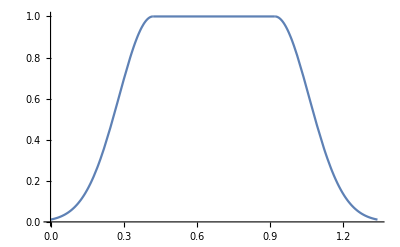

```mathematica
sigmaIn=0.14
sigmaOut=0.14
startFlat=3*sigmaIn
endFlat=startFlat+.5
endPlasma=endFlat+3*sigmaOut
f[x_]:=HeavisideTheta[startFlat-x] Exp[-(x-startFlat)^2/(2 sigmaIn^2)]+HeavisideTheta[x-startFlat] HeavisideTheta[endFlat-x]+HeavisideTheta[x-endFlat] Exp[-(x-endFlat)^2/(2 sigmaOut^2)];
Plot[f[x],{x,0,endPlasma}]
```